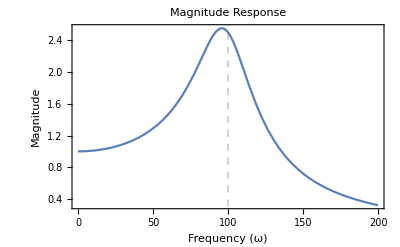

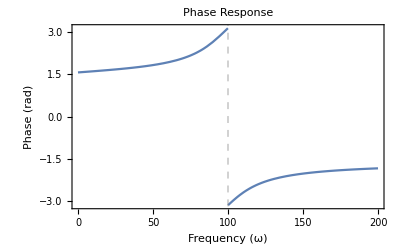

```mathematica
(*Define system parameters*)
ωn= 100;
(*Undamped natural frequency*)
ζ=0.2;
(*Damping ratio*)(*Frequency response function*)
FRF[ω_]:=Module[{β},β=ω/ωn;
{1/Sqrt[(1-β^2)^2+(2 ζ β)^2],ArcTan[-2 ζ β,1-β^2]}];

(*Plot magnitude and phase*)
Plot[FRF[ω][[1]],{ω,0,2 ωn},Frame->True,FrameLabel->{"Frequency (ω)","Magnitude"},PlotLabel->"Magnitude Response",GridLines->{{ωn},None},GridLinesStyle->Directive[Gray,Dashed]]

Plot[FRF[ω][[2]],{ω,0,2 ωn},Frame->True,FrameLabel->{"Frequency (ω)","Phase (rad)"},PlotLabel->"Phase Response",GridLines->{{ωn},None},GridLinesStyle->Directive[Gray,Dashed]]
```

```mathematica
Plot3D[η,{r1,-8,8},{r2,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[ζ,{r1,-8,8},{r2,-8,8}]
```

-Graphics3D-